```mathematica
Traverse23Four[key_,prop_:"atleast"]:=Block[{todo={key},current,edges={},children,fibos=Table[Fibonacci[k],{k,0,100}],append},
While[todo≠{},
current=First[todo];
todo=Rest[todo];
children=allGraphs4[current,"children"];
children=Select[children,(*allGraphs5[#[[1]],prop]+allGraphs5[#[[2]],prop]==allGraphs5[current,prop]&&*)MemberQ[fibos,allGraphs4[#[[1]],prop]]&&MemberQ[fibos,allGraphs4[#[[2]],prop]] &];
If[children≠{},
children=First[children];
append=Sort[{current->children[[1]],current->children[[2]]},allGraphs4[#1[[2]],prop]<allGraphs4[#2[[2]],prop]&];
(*Table[If[allGraphs5[k,"atleast"]==3,Print[ShowGraph5Least[k]]],{k,Map[Last,append]}];*)
edges=Join[edges,append];
todo=Join[todo,children]
];
];
edges
]
```

```mathematica
Traverse23Four[0]
```

{0→486,0→243,243→300,243→270,486→666,486→576,270→369,270→279,300→473,300→382,576→637,576→606,666→728,666→697,279→442,279→360,369→377,369→373,382→400,382→391,606→608,606→607,360→367,360→363,442→448,442→445,363→364,363→365}

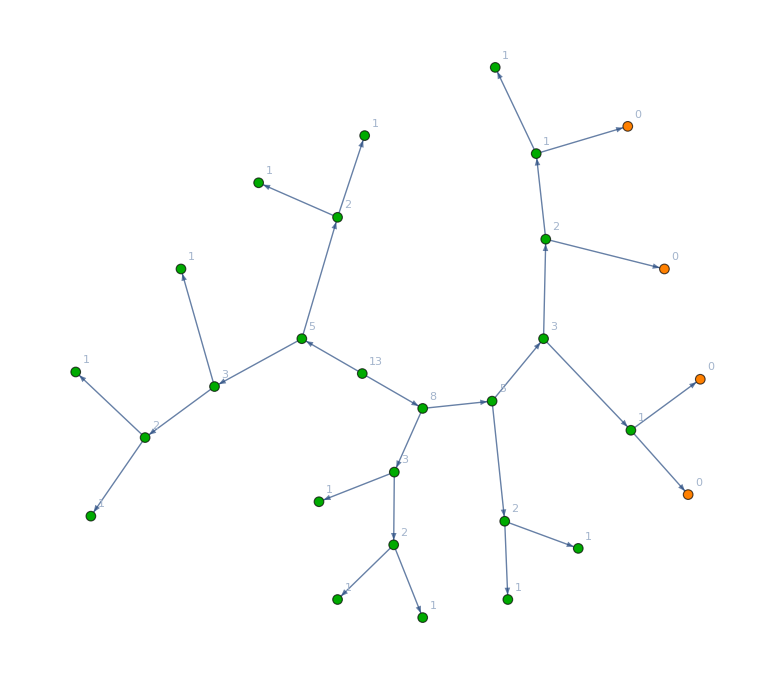

```mathematica
With[
{edges=Traverse23Four[0]},
Graph[edges,GraphLayout->"RadialEmbedding",
VertexLabels->Table[k->Tooltip[allGraphs4[k,"atleast"],Labeled[ShowGraph4Least[k],allGraphs4[k,"atleastwhy"]]],{k,VertexList[edges]}],
VertexStyle->Table[k->ColourForKey[allGraphs4,k],{k,VertexList[edges]}]
]
]
```

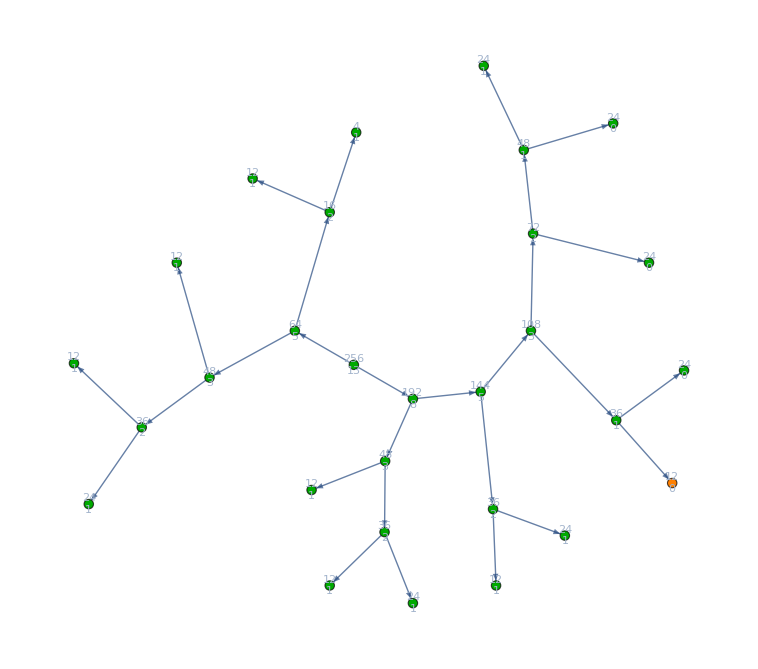

```mathematica
With[
{edges=Traverse23Four[0]},
Graph[edges,GraphLayout->"RadialEmbedding",
VertexLabels->Table[k->Placed[Tooltip[Framed[Style[Column[{ChromaticPolynomial[allGraphs4[k,"graph"],4],allGraphs4[k,"atleast"]}],Magnification->1],Background->White,FrameStyle->ColourForKey[allGraphs4,k]],Labeled[ShowGraph4Least[k],allGraphs4[k,"atleastwhy"]]],Center],{k,VertexList[edges]}],
VertexStyle->Table[k->ColourForKey[allGraphs5,k],{k,VertexList[edges]}]
]
]
```